```mathematica
ClearAll["Global`*"];
```

## Memory from BOB model

```mathematica
(*Computing the final spin of the blackholes*)
p0 = 0.04826; p1=0.01559; p2 = 0.00485; s4 = -0.1229; s5 = 0.4537; t0 = -2.8904; t2 = -3.5171; t3 = 2.5763; q=1; eta = 1/4; theta = π/2; 
pct= 0.99; tcut = 200; tmin = -20; tmax = 50;
```

```mathematica
Mf[α1_, α2_]:= 1- p0 - p1 (α1+ α2) - p2(α1+ α2)^2
αb[α1_, α2_]:= (q^2 α1+ α2)/(q^2+1)
```

```mathematica
Alpha[α1_, α2_]:= αb[α1, α2] + s4 eta  αb[α1, α2]^2 + s5 eta^2 αb[α1, α2]  + t0 eta αb[α1, α2]  + 2 √3 eta +  t2 eta^2 + t3 eta^3
```

```mathematica
(*ISCO calcualtion*)
Z1[af_]:= 1 + (1-af^2)^(1/3)((1+af)^(1/3) + (1-af)^(1/3))
Z2[af_, Z1_]:= √(3 af^2 + Z1^2)
RISCO[Z1_, Z2_]:= 3 + Z2 - √((3-Z1)(3+ Z1 + 2 Z2))
OMISCO[RISCO_, af_]:= 1/(RISCO^(3/2)+ af )
OMQNM[α1_, α2_]:= (1- 0.63 (1-Alpha[α1, α2])^0.3)/(2Mf[α1, α2])
```

```mathematica
(*BOB memory calculation*)
Y20[θ_]:=1/4 √(15/(2 π))Sin[θ]^2
Q[af_] := 2 (1-af)^-0.45
```

```mathematica
TAO[α1_, α2_]:= 2 Q[Alpha[α1, α2]]Mf[α1, α2]/(1- 0.63 (1-Alpha[α1, α2])^0.3)
```

```mathematica
Ap[α1_, α2_] := 1.068(1-Mf[α1, α2])^0.8918
OMREF[α1_, α2_]:= OMISCO[RISCO[Z1[Alpha[α1, α2]], Z2[Alpha[α1, α2], Z1[Alpha[α1, α2]]]],Alpha[α1, α2]](1-Alpha[α1, α2])
```

```mathematica
OMP[α1_, α2_]:= ((OMQNM[α1, α2]^4 + OMREF[α1, α2]^4)/2)^(1/4)
OMM[α1_, α2_]:= ((OMQNM[α1, α2]^4 - OMREF[α1, α2]^4)/2)^(1/4)
```

```mathematica
(*Slight consusion over sign*)
KAPPAM[α1_, α2_]:= ((OMP[α1, α2]^4 + OMM[α1, α2]^4))^(1/4)
KAPPAP[α1_, α2_]:= ((OMP[α1, α2]^4 - OMM[α1, α2]^4))^(1/4)
(*BOB Memory*)
OM[t_, α1_, α2_]:= (OMP[α1, α2]^4 + OMM[α1, α2]^4 Tanh[t/TAO[α1, α2]])^(1/4)
```

```mathematica
MEMBOB[t_, α1_, α2_]:= (Sin[theta]^2)((17 + (Cos[theta])^2)/192/π)Ap[α1, α2]^2 TAO[α1, α2]OM[t, α1, α2]^2/OMM[α1, α2]^4
```

```mathematica
BOBmemScale[scale_]:= Plot[MEMBOB[t, scale, scale], {t, -200, 50}, PlotRange->{{-200, 50},{-0.004,0.15}}]
```

```mathematica
Manipulate[BOBmemScale[n], {n, -0.99, 0.99}]
```

```mathematica
(*Importing NR memory data. Here the files are names in such a way i.e NRdataSm0p2 = NRdata + Sm0p2. Where Sm0p2 mean Spin -0.2. All files are named accoringly *)
filelocation="/home/aschoudhary/gravitational_wave_memory_project/data"
NRdataSm0p2= Import[filelocation<>"/SXSdata/Spinning_binary_with_SpinAntialigned_27Dec/Memory_data/rMPsi4_Sz1_m0p20_Sz2_m0p20_q1p5dataN4Clean_hMemNR.dat"];
NRdataSm0p43= Import[filelocation<>"/SXSdata/Spinning_binary_with_SpinAntialigned_27Dec/Memory_data/rMPsi4_Sz1_m0p43_Sz2_m0p43_q1p5dataN4Clean_hMemNR.dat"];
NRdataSm0p60= Import[filelocation<>"/SXSdata/Spinning_binary_with_SpinAntialigned_27Dec/Memory_data/rMPsi4_Sz1_m0p60_Sz2_m0p60_q1p5dataN4Clean_hMemNR.dat"];
NRdataSm0p80= Import[filelocation<>"/SXSdata/Spinning_binary_with_SpinAntialigned_27Dec/Memory_data/rMPsi4_Sz1_m0p80_Sz2_m0p80_q1p5dataN4Clean_hMemNR.dat"];
NRdataSm0p90= Import[filelocation<>"/SXSdata/Spinning_binary_with_SpinAntialigned_27Dec/Memory_data/rMPsi4_Sz1_m0p90_Sz2_m0p90_q1p5dataN4Clean_hMemNR.dat"];
NRdataSm0p94= Import[filelocation<>"/SXSdata/Spinning_binary_with_SpinAntialigned_27Dec/Memory_data/rMPsi4_Sz1_m0p94_Sz2_m0p94_q1p5dataN4Clean_hMemNR.dat"];
NRdataS0p0= Import[filelocation<>"/SXSdata/Spinning_binary_with_SpinAligned_27Dec/Memory_data/rMPsi4_Sz1_0p00_Sz2_0p00_q1p5dataN4Clean_hMemNR.dat"];
NRdataS0p2=Import[filelocation<>"/SXSdata/Spinning_binary_with_SpinAligned_27Dec/Memory_data/rMPsi4_Sz1_0p20_Sz2_0p20_q1p5dataN4Clean_hMemNR.dat"];
NRdataS0p6=Import[filelocation<>"/SXSdata/Spinning_binary_with_SpinAligned_27Dec/Memory_data/rMPsi4_Sz1_0p60_Sz2_0p60_q1p5dataN4Clean_hMemNR.dat"];
NRdataS0p8=Import[filelocation<>"/SXSdata/Spinning_binary_with_SpinAligned_27Dec/Memory_data/rMPsi4_Sz1_0p80_Sz2_0p80_q1p5dataN4Clean_hMemNR.dat"];
NRdataS0p99=Import[filelocation<>"/SXSdata/Spinning_binary_with_SpinAligned_27Dec/Memory_data/rMPsi4_Sz1_0p99_Sz2_0p99_q1p5dataN4Clean_hMemNR.dat"];
```

/home/aschoudhary/gravitational_wave_memory_project/data

```mathematica
(*here a factor of 17 is multipled. This is done because I missed this factor while saving the memory data from Matlab code*)
(*Puting data into a table to do List plot. Also plots below are shifted such the the maximum occurs at y=0*)
```

```mathematica
hmemNRSm0p2= Transpose[{NRdataSm0p2[[All,1]],(17 NRdataSm0p2[[All,2]]-Max[17 NRdataSm0p2[[All,2]]])}];
hmemNRSm0p43= Transpose[{NRdataSm0p43[[All,1]],(17 NRdataSm0p43[[All,2]]-Max[17 NRdataSm0p43[[All,2]]])}];
hmemNRSm0p60= Transpose[{NRdataSm0p60[[All,1]],(17 NRdataSm0p60[[All,2]]-Max[17 NRdataSm0p60[[All,2]]])}];
hmemNRSm0p80= Transpose[{NRdataSm0p80[[All,1]],(17 NRdataSm0p80[[All,2]]-Max[17 NRdataSm0p80[[All,2]]])}];
hmemNRSm0p90= Transpose[{NRdataSm0p90[[All,1]],(17 NRdataSm0p90[[All,2]]-Max[17 NRdataSm0p90[[All,2]]])}];
hmemNRSm0p94= Transpose[{NRdataSm0p94[[All,1]],(17 NRdataSm0p94[[All,2]]-Max[17 NRdataSm0p94[[All,2]]])}];
hmemNRS0p0= Transpose[{NRdataS0p0[[All,1]],(17 NRdataS0p0[[All,2]]-Max[17 NRdataS0p0[[All,2]]])}];
hmemNRS0p2= Transpose[{NRdataS0p2[[All,1]],(17 NRdataS0p2[[All,2]]-Max[17 NRdataS0p2[[All,2]]])}];
hmemNRS0p6= Transpose[{NRdataS0p6[[All,1]],(17 NRdataS0p6[[All,2]]-Max[17 NRdataS0p6[[All,2]]])}];
hmemNRS0p8= Transpose[{NRdataS0p8[[All,1]],(17 NRdataS0p8[[All,2]]-Max[17 NRdataS0p8[[All,2]]])}];
hmemNRS0p99= Transpose[{NRdataS0p99[[All,1]],(17 NRdataS0p99[[All,2]]-Max[17 NRdataS0p99[[All,2]]])}];
```

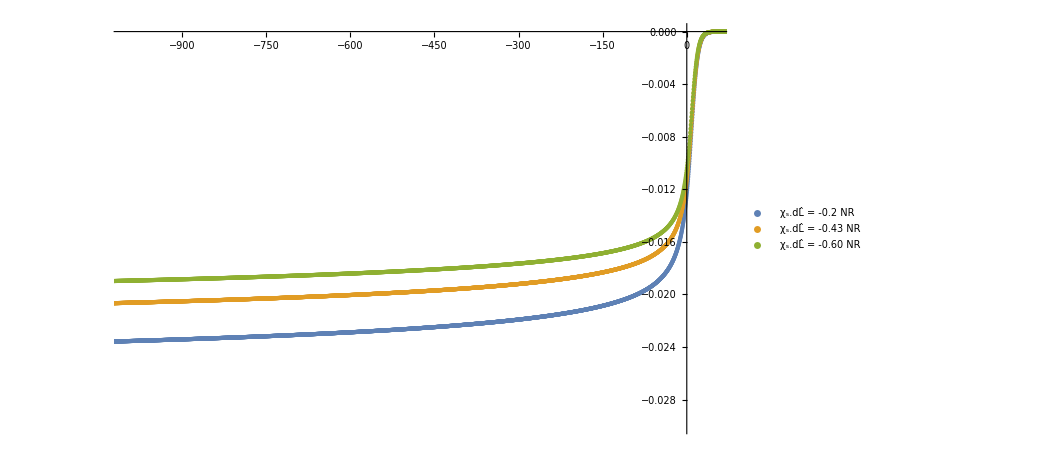

```mathematica
ListPlot[{hmemNRSm0p2, hmemNRSm0p43, hmemNRSm0p60},PlotRange->{{-1000.05,50.0},{-0.03, 0.00}}, PlotLegends->Placed[{"χ_s.dL̂ = -0.2 NR", "χ_s.dL̂ = -0.43 NR", "χ_s.dL̂ = -0.60 NR"},{0.120,0.1}], PlotStyle->PointSize[Medium]]
```

```mathematica
(*Below I renormalize data all data in such a way that the amplitude in between -1 and 0.  I devided memory amplitude by the Max(hmem)- Min(hmem)*)
```

```mathematica
hmemNRSm0p2Norm= Transpose[{NRdataSm0p2[[All,1]],(17 NRdataSm0p2[[All,2]]-Max[17 NRdataSm0p2[[All,2]]])/(Max[17 NRdataSm0p2[[All,2]]]-Min[17 NRdataSm0p2[[All,2]]])}];
hmemNRSm0p43Norm= Transpose[{NRdataSm0p43[[All,1]],(17 NRdataSm0p43[[All,2]]-Max[17 NRdataSm0p43[[All,2]]])/(Max[17 NRdataSm0p43[[All,2]]]-Min[17 NRdataSm0p43[[All,2]]])}];
hmemNRSm0p60Norm= Transpose[{NRdataSm0p60[[All,1]],(17 NRdataSm0p60[[All,2]]-Max[17 NRdataSm0p60[[All,2]]])/(Max[17 NRdataSm0p60[[All,2]]]-Min[17 NRdataSm0p60[[All,2]]])}];
hmemNRSm0p80Norm= Transpose[{NRdataSm0p80[[All,1]],(17 NRdataSm0p80[[All,2]]-Max[17 NRdataSm0p80[[All,2]]])/(Max[17 NRdataSm0p80[[All,2]]]-Min[17 NRdataSm0p80[[All,2]]])}];
hmemNRSm0p90Norm= Transpose[{NRdataSm0p90[[All,1]],(17 NRdataSm0p90[[All,2]]-Max[17 NRdataSm0p90[[All,2]]])/(Max[17 NRdataSm0p90[[All,2]]]-Min[17 NRdataSm0p90[[All,2]]])}];
hmemNRSm0p94Norm= Transpose[{NRdataSm0p94[[All,1]],(17 NRdataSm0p94[[All,2]]-Max[17 NRdataSm0p94[[All,2]]])/(Max[17 NRdataSm0p94[[All,2]]]-Min[17 NRdataSm0p94[[All,2]]])}];
hmemNRS0p0Norm= Transpose[{NRdataS0p0[[All,1]],(17 NRdataS0p0[[All,2]]-Max[17 NRdataS0p0[[All,2]]])/(Max[17 NRdataS0p0[[All,2]]]-Min[17 NRdataS0p0[[All,2]]])}];
hmemNRS0p2Norm= Transpose[{NRdataS0p2[[All,1]],(17 NRdataS0p2[[All,2]]-Max[17 NRdataS0p2[[All,2]]])/(Max[17 NRdataS0p2[[All,2]]]-Min[17 NRdataS0p2[[All,2]]])}];
hmemNRS0p6Norm= Transpose[{NRdataS0p6[[All,1]],(17 NRdataS0p6[[All,2]]-Max[17 NRdataS0p6[[All,2]]])/(Max[17 NRdataS0p6[[All,2]]]-Min[17 NRdataS0p6[[All,2]]])}];
hmemNRS0p8Norm= Transpose[{NRdataS0p8[[All,1]],(17 NRdataS0p8[[All,2]]-Max[17 NRdataS0p8[[All,2]]])/(Max[17 NRdataS0p8[[All,2]]]-Min[17 NRdataS0p8[[All,2]]])}];
hmemNRS0p99Norm= Transpose[{NRdataS0p99[[All,1]],(17 NRdataS0p99[[All,2]]-Max[17 NRdataS0p99[[All,2]]])/(Max[17 NRdataS0p99[[All,2]]]-Min[17 NRdataS0p99[[All,2]]])}];
```

```mathematica
BOBmemScaleShift[scale_, timeShift_]:= Show[Plot[(MEMBOB[t+timeShift, scale, scale]-MEMBOB[300, scale, scale])/(MEMBOB[300, scale, scale]), {t, -20,70}, PlotRange->{{-10,70},{-1.1004,0.10}}, PlotStyle->Black],ListPlot[{hmemNRSm0p80Norm, hmemNRS0p2Norm, hmemNRS0p6Norm,  hmemNRS0p8Norm},PlotRange->{{-10.05,50.0},{-0.06, 0.00}}, PlotLegends->Placed[{"χ_s.dL̂ = -0.80 NR","χ_s.dL̂ = 0.20 NR", "χ_s.dL̂ = 0.60 NR",  "χ_s.dL̂ = 0.80 NR"},{0.120,0.7}], PlotStyle->{PointSize[Small], Opacity[0.9]}]]
```

```mathematica
Manipulate[BOBmemScaleShift[n,timeshift], {n, -0.94, 0.99}, {timeshift, -20,0}]
```

```mathematica
BOBmemScaleOriginal[scale_, timeShift_]:= Show[Plot[(MEMBOB[t+timeShift, scale, scale]-MEMBOB[300, scale, scale])((0.2)/MEMBOB[300, scale, scale]), {t, -20,70}, PlotRange->{{-20,70},{-0.1004,0.10}}, PlotStyle->Black],ListPlot[{hmemNRSm0p94, hmemNRS0p2, hmemNRS0p6,  hmemNRS0p99},PlotRange->{{-20.05,50.0},{-0.06, 0.00}}, PlotLegends->Placed[{"χ_s.dL̂ = -0.94 NR","χ_s.dL̂ = 0.20 NR", "χ_s.dL̂ = 0.60 NR",  "χ_s.dL̂ = 0.99 NR"},{0.120,0.7}], PlotStyle->{PointSize[Small], Opacity[0.5]}]]
```

```mathematica
Manipulate[BOBmemScaleOriginal[n,timeshift], {n, -0.94, 0.99}, {timeshift, -20,0}]
```